```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Verdana",FontSize->12}];
```

```mathematica
pressure = 95100;
deltaPressure = +149.112;
density= 1.204;
```

```mathematica
(*upp={{0,-0.1},{18,-0.1},{39.5,-1.0},{60,-5.6},{79,-14.6},{90,-13},{100,0.5},{102,15.5}};
lowp ={{102,15.5},{100,5.4},{91,-8.8},{85,-7.5},{67.5,-0.8},{42.5,2.3},{19.5,1.5},{0,1.5}}//Reverse;*)
upp={{0,-0.1},{18,-0.1},{39.5,-1.0},{60,-5.6},{79,-14.6},{90,-13},{100,0.5}};
lowp ={{100,5.4},{91,-8.8},{85,-7.5},{67.5,-0.8},{42.5,2.3},{19.5,1.5},{0,1.5}}//Reverse;

upspeeds = Table[{upp[[i]][[1]],Sqrt[2*(deltaPressure-upp[[i]][[2]]*9.81)/density]},{i,1,Length[upp]}];
downspeeds = Table[{lowp[[i]][[1]],Sqrt[2*(deltaPressure-lowp[[i]][[2]]*9.81)/density]},{i,1,Length[lowp]}];
upspeeds
downspeeds
```

{{0,15.79},{18,15.79},{39.5,16.2478},{60,18.4106},{79,22.0366},{90,21.4368},{100,15.4773}}

{{0,14.9416},{19.5,14.9416},{42.5,14.4988},{67.5,16.1472},{85,19.2331},{91,19.7762},{100,12.6372}}

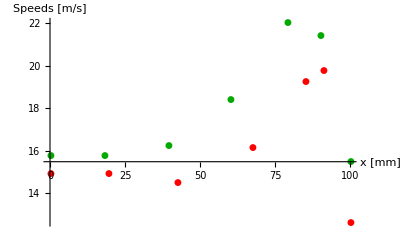

```mathematica
vup=ListPlot[upspeeds,PlotStyle->{Thick,Darker[Green]},PlotMarkers->Automatic, PlotRange->All];
vlow=ListPlot[downspeeds,PlotStyle->{Thick,Red},PlotMarkers->Automatic, PlotRange -> All];
comb=Show[vup,vlow,AxesLabel->{"x [mm]","Speeds [m/s]"} ]
```

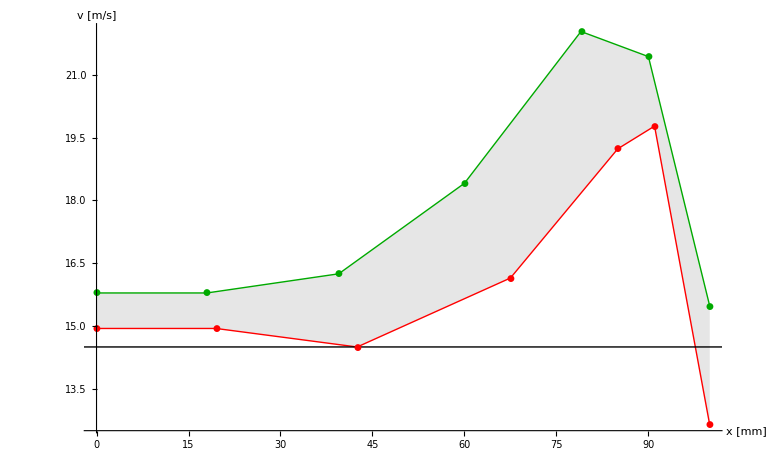

0.0366675

```mathematica
uvint=Interpolation[upspeeds, InterpolationOrder->1];
lvint=Interpolation[downspeeds, InterpolationOrder->1];
vp=Plot[{uvint[x],lvint[x]},{x,0,100},PlotStyle->{{Thick,Darker[Green]},{Thick,Red}},Filling->{1->{2}},FillingStyle->{Lighter[Gray,0.8]}];
Show[vp,comb,AxesLabel->{"x [mm]","v [m/s]"},Epilog->Line[{{-5,14.5},{105,14.5}}]]
intdiff=NIntegrate[uvint[x],{x,0,100}]*0.001-NIntegrate[lvint[x],{x,0,100}]*0.001;
lift = 0.01*density*intdiff*14.76
```

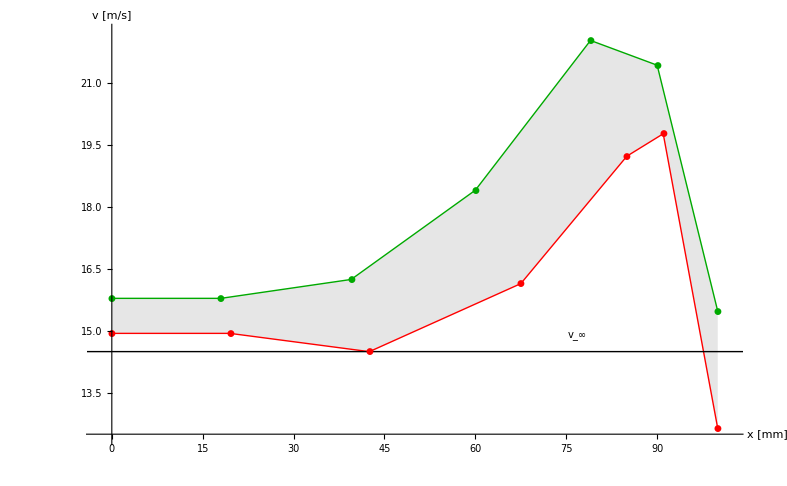

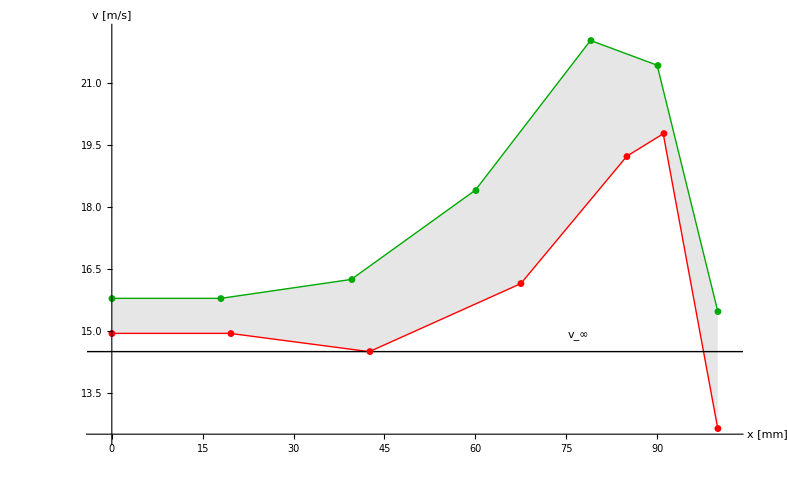

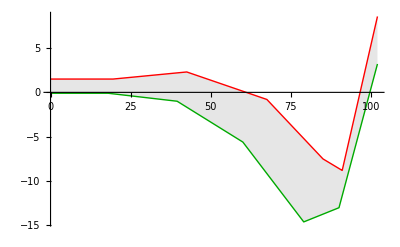

0.621608

```mathematica
order:=1;
uint=Interpolation[upp,InterpolationOrder->order];
lint=Interpolation[lowp,InterpolationOrder->order];
ip=Plot[{uint[x],lint[x]},{x,0,102},PlotStyle->{{Thick,Darker[Green]},{Thick,Red}},Filling->{1->{2}},FillingStyle->{Lighter[Gray,0.8]}]
intdiff=0.14*9.81*0.001*NIntegrate[lint[x]-uint[x],{x,0,102}]
```

Show::gcomb: Could not combine the graphics objects in GraphicsBox[GraphicsComplexBox[List[List[2.0816326530612247`*^-6, -0.1`], List[2.0021234425561003`, -0.1`], List[4.172652422716782`, -0.1`], List[6.199344124155513`, -0.1`], List[8.186280179525356`, -0.1`], List[10.341623854132434`, -0.1`], List[12.353130250017562`, -0.1`], List[14.533044265139925`, -0.1`], List[16.673202634193398`, -0.1`], List[18.66952372452492`, -0.12802657451499677`], List[20.834252434093678`, -0.21864312514810746`], List[22.855143864940484`, -0.30323858039285745`], List[24.836279649718403`, -0.38616984580216573`], List[26.985823053733554`, -0.4761507324818697`], List[28.991529179026756`, -0.560110523773213`], List[31.165642923557193`, -0.6511199363349522`], List[33.30000102201875`, -0.7404651590612499`], List[35.29052184175835`, -0.8237892863991867`], List[37.449450280735185`, -0.9141630350075194`], List[39.46454144099007`, -0.9985156882274913`], List[41.64804022048219`, -1.4819992689862467`], List[43.791783353905416`, -1.9630343135592638`], List[45.7916892086067`, -2.4117936760776004`], List[47.960002682545216`, -2.8983420653516094`], List[49.98447887776178`, -3.352614772570936`], List[51.969199426909455`, -3.797966700672365`], List[54.122327595294365`, -4.281107655529468`], List[56.13161848495733`, -4.7319729283318885`], List[58.30931699385752`, -5.22062722788998`], List[60.44725985668883`, -5.8118599321157625`], List[62.44136544079819`, -6.75643626143072`], List[64.60387864414477`, -7.780784620910681`], List[66.6225545687694`, -8.73699953257498`], List[68.60147484732515`, -9.674382822417176`], List[70.74880274511813`, -10.691538142424376`], List[72.75229336418916`, -11.640560014615916`], List[74.92419160249742`, -12.66935391697246`], List[76.95225256208373`, -13.630014371513345`], List[78.94055787560116`, -14.571843204232128`], List[81.09727080835582`, -14.294942427875517`], List[83.11014646238853`, -14.002160514561668`], List[85.29142973565847`, -13.684882947540586`], List[87.43295736285953`, -13.373388019947706`], List[89.43064771133864`, -13.082814878350744`], List[91.59674567905498`, -10.844393333275782`], List[93.61900636804937`, -8.114341403133352`], List[95.60151141097487`, -5.437959595183933`], List[97.7524240731376`, -2.534227501264235`], List[99.7594994565784`, 0.17532426638083504`], List[101.99999791836734`, 3.1999971897959116`], Skeleton[456]], List[List[List[], List[], List[], List[], List[], List[], List[EdgeForm[], RGBColor[0.9`, 0.9`, 0.9`], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[]], List[List[], List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], RGBColor[0, NCache[Rational[2, 3], 0.6666666666666666`], 0], LineBox[List[Skeleton[252]]]], List[Hue[0.9060679774997897`, 0.6`, 0.6`], Thickness[Large], RGBColor[1, 0, 0], LineBox[List[Skeleton[254]]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], Rule[BaseStyle, List[Rule[FontFamily, .

Show[-Graphics-,pup,plow,AxesLabel→{x [mm],Pressure [mmWs]}]

Show[-Graphics-,pup,plow,AxesLabel→{x [mm],Pressure [mmWs]}]

Show[-Graphics-,ListPlot[up,PlotStyle→{Thickness[Large],RGBColor[0,2/3,0]},PlotMarkers→Automatic],ListPlot[low,PlotStyle→{Thickness[Large],RGBColor[1,0,0]},PlotMarkers→Automatic],AxesLabel→{x [mm],Pressure [mmWs]}]

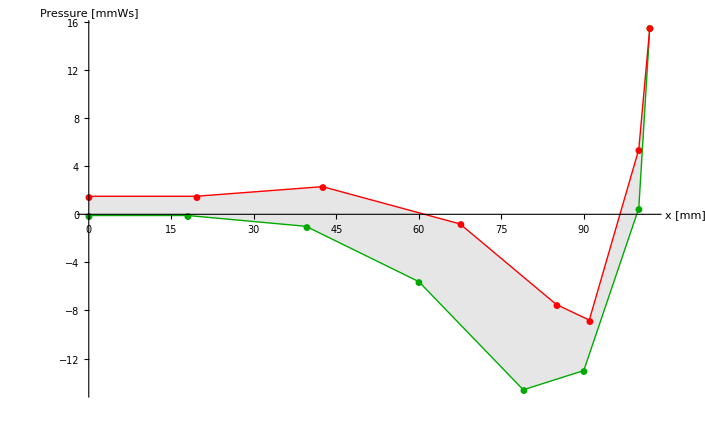

```mathematica
Show[ip,pup,plow,AxesLabel->{"x [mm]","Pressure [mmWs]"}]
```